# Using Mathematica To Find Reflection and Transmission Coefficients

In this notebook we'll demonstrate how to use Mathematica to compute reflection and transmission coefficients.  As an example, we'll compute and plot T and R for problem 3(a) of pset 9.

Using the continuity conditions for the finite well, one obtains the following equations that need to be solved simultaneously:
A ⅇ^(-ⅈ k L/2)+B ⅇ^(ⅈ k L/2)==C ⅇ^(-ⅈ q L/2)+D ⅇ^(ⅈ q L/2)
C ⅇ^(ⅈ q L/2)+D ⅇ^(-ⅈ q L/2)==F ⅇ^(ⅈ k L/2)
k(A ⅇ^(-ⅈ k L/2)-B ⅇ^(ⅈ k L/2))==q (C ⅇ^(-ⅈ q L/2)-D ⅇ^(ⅈ q L/2) )
q (C ⅇ^(ⅈ q L/2)-D ⅇ^(-ⅈ q L/2))==F k ⅇ^(ⅈ k L/2),
where k=(√(2 μ E))/ℏand q=(√(2 μ (E+V0)))/ℏ.  In setting up these equations I centered my well on x=0 (so the well goes from -L/2 to +L/2).  The final answers will not depend on where I place my well, but the initial equations may look a little different.

In solving this set of equations, Mathematica will actually be smart enough to realize that I have five unknowns (A, B, C, D, E) but only four equations.  It will therefore express everything in terms of ratios of coefficients.  However, it is easier to simply set A=1.  To solve the equations, we use the command Solve.  The basic syntax of Solve is Solve[{eqn1, eqn2, eqn3...}, {var1, var2, ...}], where eqn1 is the first equation (be sure to use double equal signs == in your equations), var1 is the first variable you want to solve for, and so on.

```mathematica
Solutions=Solve[{ⅇ^(-ⅈ k L/2)+B ⅇ^(ⅈ k L/2)==C ⅇ^(-ⅈ q L/2)+D ⅇ^(ⅈ q L/2), C ⅇ^(ⅈ q L/2)+D ⅇ^(-ⅈ q L/2)==F ⅇ^(ⅈ k L/2),k(ⅇ^(-ⅈ k L/2)-B ⅇ^(ⅈ k L/2))==q (C ⅇ^(-ⅈ q L/2)-D ⅇ^(ⅈ q L/2) ),q (C ⅇ^(ⅈ q L/2)-D ⅇ^(-ⅈ q L/2))==F k ⅇ^(ⅈ k L/2)}, {B, C, D, F}]
```

{{B→(ⅇ^(-ⅈ k L) (-1+ⅇ^(2 ⅈ L q)) (k^2-q^2))/(-k^2+ⅇ^(2 ⅈ L q) k^2-2 k q-2 ⅇ^(2 ⅈ L q) k q-q^2+ⅇ^(2 ⅈ L q) q^2),C→-(2 ⅇ^(-1/2 ⅈ k L+(ⅈ L q)/2) k (k+q))/(-k^2+ⅇ^(2 ⅈ L q) k^2-2 k q-2 ⅇ^(2 ⅈ L q) k q-q^2+ⅇ^(2 ⅈ L q) q^2),D→(2 ⅇ^(-1/2 ⅈ k L+(3 ⅈ L q)/2) k (k-q))/(-k^2+ⅇ^(2 ⅈ L q) k^2-2 k q-2 ⅇ^(2 ⅈ L q) k q-q^2+ⅇ^(2 ⅈ L q) q^2),F→-(4 ⅇ^(-ⅈ k L+ⅈ L q) k q)/(-k^2+ⅇ^(2 ⅈ L q) k^2-2 k q-2 ⅇ^(2 ⅈ L q) k q-q^2+ⅇ^(2 ⅈ L q) q^2)}}

This gives us our solutions.  Next we need to do a little housekeeping.  Because of the way Mathematica works, we need to "tell" it that we want it to store certain results.  In what follows, the "/." command tells Mathematica to look at the vector called Solutions and to replace B with whatever B is in that vector.  (The [[1]] symbol tells Mathematica to look at the first element of the solutions vector, and is an annoying complication that arises because Mathematica decided to use double braces {{}} for the vector, so the entire vector is technically stored in the first element).

```mathematica
BoverA=B/.Solutions[[1]]
```

(ⅇ^(-ⅈ k L) (-1+ⅇ^(2 ⅈ L q)) (k^2-q^2))/(-k^2+ⅇ^(2 ⅈ L q) k^2-2 k q-2 ⅇ^(2 ⅈ L q) k q-q^2+ⅇ^(2 ⅈ L q) q^2)

```mathematica
FoverA=F/.Solutions[[1]]
```

-(4 ⅇ^(-ⅈ k L+ⅈ L q) k q)/(-k^2+ⅇ^(2 ⅈ L q) k^2-2 k q-2 ⅇ^(2 ⅈ L q) k q-q^2+ⅇ^(2 ⅈ L q) q^2)

If we want, we can use the FullSimplify command to simplify the results (even though we really don't care about simplifying now that Mathematica's doing all the heavy algebraic lifting for us):

```mathematica
BoverA=FullSimplify[BoverA]
```

(ⅇ^(-ⅈ k L) (k-q) (k+q) Sin[L q])/(2 ⅈ k q Cos[L q]+(k^2+q^2) Sin[L q])

```mathematica
FoverA=FullSimplify[FoverA]
```

-(4 ⅇ^(-ⅈ L (k-q)) k q)/(ⅇ^(2 ⅈ L q) (k-q)^2-(k+q)^2)

Getting the transmission and reflection coefficients can be somewhat yucky because Mathematica doesn't always know what quantities are real and what quantities are imaginary.  The follow commands seem to do the trick:

```mathematica
Transcoeff=FullSimplify[ComplexExpand[FoverA*Conjugate[FoverA]]]
```

(8 k^2 q^2)/(k^4+6 k^2 q^2+q^4-(k^2-q^2)^2 Cos[2 L q])

```mathematica
Reflcoeff=FullSimplify[ComplexExpand[BoverA*Conjugate[BoverA]]]
```

(2 (k^2-q^2)^2 Sin[L q]^2)/(k^4+6 k^2 q^2+q^4-(k^2-q^2)^2 Cos[2 L q])

We can now ask Mathematica to non-dimensionalize the expressions:

```mathematica
T[x_,g0_]=FullSimplify[Transcoeff/.k->(√(2 μ En))/ℏ/.q->(√(2 μ (En+V0)))/ℏ/.En->x V0/.L ->(g0 ℏ)/(√(2 μ)√V0)];
```

```mathematica
R[x_,g0_]=FullSimplify[Reflcoeff/.k->(√(2 μ En))/ℏ/.q->(√(2 μ (En+V0)))/ℏ/.En->x V0/.L ->(g0 ℏ)/(√(2 μ)√V0)];
```

Plotting the results for g0 = 20:

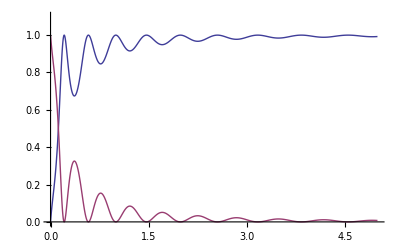

```mathematica
Geenought=20;
Plot[{T[x, Geenought], R[x,Geenought]}, {x, 0, 5}, PlotRange->{0, 1.1}]
```

Plotting the functions for general g0 using Mathematica's new dynamic capabilities:

```mathematica
Manipulate[Plot[{T[x, g0], R[x,g0]}, {x, 0, 5}, PlotRange->{0, 1.1}], {g0, 0, 50}]
```